```mathematica
FullSimplify[D[(f[r]/Sqrt[r^2-(f[r])^2])*r,r]/r]*B*r
```

(B (-f[r]^3+r^3 f'[r]))/((r^2-f[r]^2)^(3/2))

{{f→InterpolatingFunction[{{0.,400.}},<>]}}

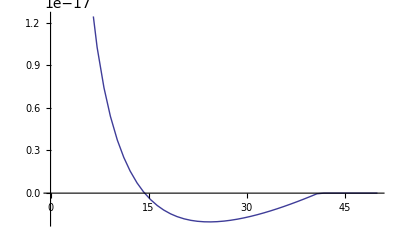

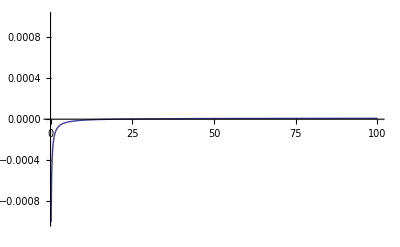

```mathematica
ClearAll[B,f,r]
B=2;
s=NDSolve[{B*(r^3*f'[r]-(f[r])^3)/Sqrt[(r^2-(f[r])^2)^3]==f'[r],f[1]==0.00001},f,{r,0,400}]
mf[x_]=Evaluate[f[x]/.s];
ρ[x_]=0.1*D[mf[x],x]/x;
dz[r_]=mf[r]/Sqrt[r^2-(mf[r])^2];
z[r_]:=NIntegrate[dz[x],{x,20,r}];
Plot[{ρ[x]},{x,0,50}]
Plot[{z[x]},{x,0,100},PlotRange->{-0.001,0.001}]
```

```mathematica
FourierTransform[r/Sqrt[r^2-2*r*rr*Cos[f]+rr^2],r,s]
```

FourierTransform[r/(√(r^2+rr^2-2 r rr Cos[f])),r,{{f→InterpolatingFunction[{{0.,400.}},<>]}}]

```mathematica
ClearAll[ρ,ϵ,r,r1,ϕ]
attr=-ρ[r1]*ϵ/Sqrt[r^2+r1^2+d^2-2*r*r1*Cos[ϕ]]
rep=ρ[r1]/Sqrt[r^2+r1^2-2*r*r1*Cos[ϕ]]
(*d<<r*)
Series[attr,{d,0,3}]
approxPot1=Normal[FullSimplify[Series[attr,{d,0,3}]+rep]]
```

-(ϵ ρ[r1])/(√(d^2+r^2+r1^2-2 r r1 Cos[ϕ]))

ρ[r1]/(√(r^2+r1^2-2 r r1 Cos[ϕ]))

-(ϵ ρ[r1])/(√(r^2+r1^2-2 r r1 Cos[ϕ]))+(ϵ ρ[r1] d^2)/(2 (r^2+r1^2-2 r r1 Cos[ϕ])^(3/2))+O[d]^4

(d^2 ϵ ρ[r1])/(2 (r^2+r1^2-2 r r1 Cos[ϕ])^(3/2))-((-1+ϵ) ρ[r1])/(√(r^2+r1^2-2 r r1 Cos[ϕ]))

```mathematica
(*ϵ=1*)
approxPot2=Normal[Series[attr/.{ϵ->1},{d,0,3}]+rep]
```

(d^2 ρ[r1])/(2 (r^2+r1^2-2 r r1 Cos[ϕ])^(3/2))

```mathematica
FullSimplify[-D[rep,r]/(r-r1*Cos[ϕ])]
```

ρ[r1]/((r^2+r1^2-2 r r1 Cos[ϕ])^(3/2))

```mathematica
Series[attr+rep,{r,0,2}]
```

((√(r1^2) ρ[r1])/r1^2-(ϵ ρ[r1])/(√(d^2+r1^2)))+((√(r1^2) Cos[ϕ] ρ[r1])/r1^3-(r1 ϵ Cos[ϕ] ρ[r1])/((d^2+r1^2)^(3/2))) r+(-(√(r1^2) ρ[r1])/(2 r1^4)+(d^2 ϵ ρ[r1])/(2 (d^2+r1^2)^(5/2))+(r1^2 ϵ ρ[r1])/(2 (d^2+r1^2)^(5/2))+(3 √(r1^2) Cos[ϕ]^2 ρ[r1])/(2 r1^4)-(3 r1^2 ϵ Cos[ϕ]^2 ρ[r1])/(2 (d^2+r1^2)^(5/2))) r^2+O[r]^3

```mathematica
(1/r1-ϵ/(√(d^2+r1^2)))*ρ[r1]
```

```mathematica
ff=f/.Solve[(α^2*r^2)*(r^2-f^2)-f^2==0,f][[2]]
```

(r^2 α)/(√(1+r^2 α^2))

```mathematica
g[r_]=(FullSimplify[D[ff,r]]/r)*β
```

(α (2+r^2 α^2) β)/((1+r^2 α^2)^(3/2))

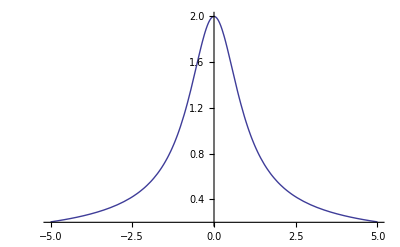

```mathematica
Plot[g[r]/.{α->1,β->1},{r,-5,5}]
```